# DNA Fourier

```mathematica
TableForm[Transpose[{{"A","T","G","C"},{1,-1,I,-I}}]]
```

A | 1
T | -1
G | ⅈ
C | -ⅈ

```mathematica
phix174genome=Import["/Users/kouamano/Downloads/phiX174.fna"];
```

```mathematica
nucleotideToComplex[
  DNA_String] := (Characters[
     ToUpperCase[StringReplace[DNA, "\n" -> ""]]] /. {"A" -> 1, "T" -> -1, "G" -> I, "C" -> -I}) /. {_String -> 0};
```

```mathematica
(phix174genomeCpx=nucleotideToComplex[phix174genome[[1]]])//Length
```

5386

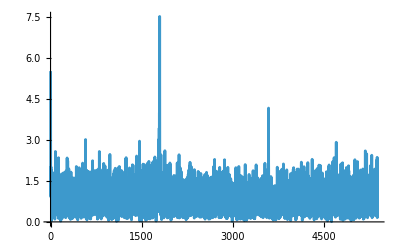

```mathematica
ListPlot[Abs[Fourier[phix174genomeCpx]],Joined->True,PlotRange->All]
```

```mathematica
Position[Abs[Fourier[phix174genomeCpx]],Max[Abs[Fourier[phix174genomeCpx]]]]
```

{{1798}}

1798 番目の要素が最も繰り返されている → (1798-1)回の繰り返し

```mathematica
5386/(1798-1)//N
```

2.99722